This document shows how to simulate a continuously monitored qubit with NDSolve. We have implemented this approach for a model that follows four quantities: three numbers that describe the qubit state (i.e., the components of the Bloch vector) and the detector's accumulated readout. The dynamical equations for these four quantities are usually written as a nonlinear stochastic differential equation in Itô form. The obstacle is that NDSolve cannot use noise as an ordinary function of time, or, more generally, any variable that must be sampled from a distribution. Following the essence of the Wong–Zakai theorem, we therefore convert the original Itô equation to its equivalent Stratonovich form, which is suited to smooth approximations of the noise, and replace the rough Wiener path with a continuous piecewise-cubic path. NDSolve can then solve the resulting random ordinary differential equation. As the noise grid is refined, this regularized equation approaches the original stochastic model under the conditions of the Wong–Zakai theorem. Symbolic checks recover the standard master-equation evolution exactly, while finite-sample simulations compare the mean and spread with independent references. These numerical comparisons support the method but do not by themselves prove convergence.

## The trajectory equations: the state and the readout in one SDE

A continuously monitored quantum state can be understood schematically as d ρ_c=ℒ(ρ_c) dt+ℳ(ρ_c) dW: the drift ℒ(ρ_c) dt describes deterministic Hamiltonian evolution, relaxation, dephasing, and the unconditional disturbance caused by measurement, while ℳ(ρ_c) dW is the stochastic, record-dependent measurement update. The detector record obeys dQ=s(ρ_c) dt+dW, where s(ρ_c) is the expected signal, so dW=dQ-s(ρ_c) dt is the innovation (the unpredictable part of the observed result) and the same Wiener increment updates both the record and the state. Because the stochastic average 𝔼[dW]=0 and d W^2=dt, dW is of order √dt; thus d ρ_c is not an ordinary time derivative but a deterministic prediction plus a random correction conditioned on what the detector reports. Averaging over all possible records removes the stochastic term and recovers the master equation.

Continuous homodyne monitoring of a driven qubit produces two coupled equations driven by the same noise: one for the observer's running estimate of the Bloch vector {x,y,z}={⟨(σ̂)_x⟩,⟨(σ̂)_y⟩,⟨(σ̂)_z⟩}, in the convention (σ̂)_z=gg-ee that puts the ground state at z=+1 (some literature uses the opposite sign), and one for the readout Q the detector accumulates while measuring (σ̂)_z. Stacking the readout as a fourth component, the pair is a single scalar-noise Itô stochastic differential equation, a drift a⃗ times dt plus a diffusion b⃗ times one Wiener increment dW:

d(x
y
z
Q)=(-Γ_2^eff x
-Γ_2^eff y-Ω_x z
γ_1(1-z)+Ω_x y
√Γ_CI z)_(a⃗) dt + (-√Γ_CI xz-√Γ_BA y
-√Γ_CI yz+√Γ_BA x
√Γ_CI (1-z^2)
1)_(b⃗) dW.

This is the target: the process whose mean we will check against the Lindblad master equation and whose spread we will check against a native integrator. The top three rows, the Bloch state, close on their own, nothing in them depends on Q; the fourth row is the record, an integral whose drift √Γ_CI z carries the (σ̂)_z signal and whose noise is the same dW that kicks the state.

The six parameters have units of inverse time: Γ_CI is the informative (coherent-information) rate, which sharpens the conditional state toward a (σ̂)_z eigenstate; Γ_BA is the backaction rate of the orthogonal homodyne quadrature, which rotates the transverse phase; Γ_d is the measurement-induced ensemble dephasing; γ_ϕ is intrinsic pure dephasing; γ_1=1/T_1 is relaxation; and Ω_x is the Rabi frequency. One combination recurs, the effective transverse decay Γ_2^eff=γ_1/2+γ_ϕ+Γ_d. When Γ_d>0, the detector efficiency is η=(Γ_CI+Γ_BA)/(2 Γ_d), with a quantum-limited detector satisfying 0≤η≤1. The benchmark ensembles below use η=1; one deliberately unphysical example violates the admissibility condition. Numerically, time and all rates are nondimensionalized by a chosen reference rate (the representative example takes that reference to be γ_1). Throughout, the code takes a rate vector r={Γ_CI,Γ_BA,Γ_d,γ_ϕ,γ_1,Ω_x}.

For a single scalar noise, the Itô equation above is identical to a Stratonovich equation with the same diffusion and a drift lowered by one exact term (the Itô-Stratonovich conversion).

d(x
y
z
Q)=(((Γ_BA+Γ_CI)/2-Γ_2^eff-Γ_CI z^2) x-√(Γ_BA Γ_CI) yz
((Γ_BA+Γ_CI)/2-Γ_2^eff-Γ_CI z^2) y+√(Γ_BA Γ_CI) xz-Ω_x z
γ_1(1-z)+Γ_CI z(1-z^2)+Ω_x y
√Γ_CI z)dt + (-√Γ_CI xz-√Γ_BA y
-√Γ_CI yz+√Γ_BA x
√Γ_CI (1-z^2)
1)∘dW.

We feed the Stratonovich form to the random ODE because continuous, piecewise-smooth approximations of a one-dimensional Wiener path converge under the usual Wong-Zakai hypotheses to the Stratonovich solution. The fact that the driving noise is scalar matters: with several noncommuting noise channels, the limiting equation can depend on how the missing iterated integrals are approximated. At any nonzero grid spacing the ODE is only a regularized model; the equality with the target SDE is a limit statement, not an identity at finite resolution. The readout row is the same in both calculi because its diffusion coefficient is the constant one, so its conversion correction vanishes. After nondimensionalizing time, Q is dimensionless; before nondimensionalization it carries the same units as W, namely √time.

## Encoding the Stratonovich vector field

Encode the Stratonovich drift, all four rows and name the entries of the rate vector r={Γ_CI,Γ_BA,Γ_d,γ_ϕ,γ_1,Ω_x}:

```mathematica
ClearAll[driftStrat];
driftStrat[{x_, y_, z_, q_}, r_] :=
  With[{ΓCI = r[[1]], ΓBA = r[[2]], Γd = r[[3]],
    γϕ = r[[4]], γ1 = r[[5]], Ωx = r[[6]]},
   With[{Γ2 = γ1/2 + γϕ + Γd},
    {((ΓBA + ΓCI)/2 - Γ2 - ΓCI z^2) x - Sqrt[ΓBA ΓCI] y z,
     ((ΓBA + ΓCI)/2 - Γ2 - ΓCI z^2) y + Sqrt[ΓBA ΓCI] x z - Ωx z,
     γ1 (1 - z) + ΓCI z (1 - z^2) + Ωx y,
     Sqrt[ΓCI] z}]];
```

Encode the Stratonovich diffusion, the same b⃗ as the Itô form:

```mathematica
ClearAll[diffStrat];
diffStrat[{x_, y_, z_, q_}, r_] :=
  With[{ΓCI = r[[1]], ΓBA = r[[2]]},
   {-Sqrt[ΓCI] x z - Sqrt[ΓBA] y,
    -Sqrt[ΓCI] y z + Sqrt[ΓBA] x,
    Sqrt[ΓCI] (1 - z^2),
    1}];
```

To read these back as formulas, write the six rates as symbols, using string subscripts so the labels stay Γ_CI,Γ_BA,… and never collide with the Bloch x or fuse into a C·I product. The readbacks and the symbolic conversion below use x,y,z,q,Q,t, a formal noise w, the starting values, and the rate symbols themselves as unassigned variables, so clear them first:

```mathematica
ClearAll[x, y, z, q, Q, t, w, x0, y0, z0, q0, Γ, γ, Ω];
ratesSym = {Subscript[Γ, "CI"], Subscript[Γ, "BA"],
   Subscript[Γ, "d"], Subscript[γ, "ϕ"],
   Subscript[γ, "1"], Subscript[Ω, "x"]};
```

Verify that the encoded drift is the Stratonovich drift written above, by reading it back on the symbolic rates:

```mathematica
driftStrat[{x, y, z, Q}, ratesSym] // MatrixForm
```

(-y z √(Γ_BA Γ_CI)+x (-γ_1/2-γ_ϕ-z^2 Γ_CI+1/2 (Γ_BA+Γ_CI)-Γ_d)
x z √(Γ_BA Γ_CI)+y (-γ_1/2-γ_ϕ-z^2 Γ_CI+1/2 (Γ_BA+Γ_CI)-Γ_d)-z Ω_x
(1-z) γ_1+z (1-z^2) Γ_CI+y Ω_x
z √Γ_CI)

As one can see, the four rows are term for term the drift in the display equation, with Wolfram ordering each sum its own way: the state rows carry the -Γ_CI z^2 sharpening and the √(Γ_BA Γ_CI) cross term, and the readout row is the bare √Γ_CI z signal. Confirm the diffusion the same way:

```mathematica
diffStrat[{x, y, z, Q}, ratesSym] // MatrixForm
```

(-y √Γ_BA-x z √Γ_CI
x √Γ_BA-y z √Γ_CI
(1-z^2) √Γ_CI
1)

As expected, the three state rows are b⃗ and the readout row is the constant one, the additive noise that makes Q the same in both stochastic calculi. The code and the equations are one object, so from here on we compute with the code.

Fix a representative normalized benchmark, rescaled by γ_1; its readout is quantum-limited (η=1), Γ_CI+Γ_BA=2 Γ_d exactly:

```mathematica
ratesB = {0.252, 0.1, 0.176, 1., 1., 3.};
```

Start from the ground state with the readout zeroed, a four-vector: the three Bloch numbers followed by the record Q:

```mathematica
initB = {0., 0., 1., 0.};
```

Fix a short time window and the trajectory count:

```mathematica
tfB = 3.; nB = 600;
```

For the trajectory to stay a density matrix, the measurement must fit inside the total dephasing, Γ_CI+Γ_BA≤2(Γ_d+γ_ϕ), an admissibility condition derived below. For Γ_d>0 it reads η≤1+γ_ϕ/Γ_d; a physical detector with η≤1 and nonnegative intrinsic dephasing satisfies it. Confirm this set passes:

```mathematica
ratesB[[1]] + ratesB[[2]] <= 2 (ratesB[[3]] + ratesB[[4]])
```

True

The quantum-limit claim is one division away; define the efficiency and read this set's:

```mathematica
ClearAll[efficiency];
efficiency[r_] := (r[[1]] + r[[2]])/(2 r[[3]]);
efficiency[ratesB]
```

1.

The efficiency is one at the input precision, by construction.

The reference for the mean is the Lindblad master equation. Because the Itô drift a⃗ is affine in {x,y,z}, the ensemble mean obeys that drift as a closed linear ODE. Encode a⃗'s three state rows once; the symbolic conversion check below must land on this same object, so one encoding serves both:

```mathematica
ClearAll[driftIto];
driftIto[{x_, y_, z_}, r_] :=
  With[{Γd = r[[3]], γϕ = r[[4]], γ1 = r[[5]], Ωx = r[[6]]},
   With[{Γ2 = γ1/2 + γϕ + Γd},
    {-Γ2 x, -Γ2 y - Ωx z, γ1 (1 - z) + Ωx y}]];
```

Calling that encoding "the Lindblad master equation" requires a derivation. Build the generator itself, the drive H=Ω_x/2 σ_x with relaxation γ_1 𝒟[σ_-] toward the z=+1 ground state and total dephasing (γ_ϕ+Γ_d)/2 𝒟[σ_z], where 𝒟[L]ρ=Lρ L^†-1/2(L^†Lρ+ρ L^†L); project it onto the Pauli components and subtract driftIto:

```mathematica
With[{sx = PauliMatrix[1], sy = PauliMatrix[2], sz = PauliMatrix[3],
  sm = {{0, 1}, {0, 0}}, id = IdentityMatrix[2]},
 Module[{ρ, diss, gen},
  ρ = (id + x sx + y sy + z sz)/2;
  diss[L_] := L . ρ . ConjugateTranspose[L] -
    (ConjugateTranspose[L] . L . ρ + ρ . ConjugateTranspose[L] . L)/2;
  gen = -I (ratesSym[[6]]/2) (sx . ρ - ρ . sx) +
    ratesSym[[5]] diss[sm] + ((ratesSym[[4]] + ratesSym[[3]])/2) diss[sz];
  Simplify[(Tr[gen . #] & /@ {sx, sy, sz}) - driftIto[{x, y, z}, ratesSym]]]]
```

{0,0,0}

Every component cancels, so the affine drift is the Lindblad master equation in Bloch coordinates. Relaxation carries γ_1, while the σ_z dissipator carries intrinsic and measurement-induced dephasing. Solve that affine system with DSolve, building the equations from driftIto itself so the reference and the checked drift stay one object, and return ⟨v⃗⟩(t):

```mathematica
ClearAll[lindbladBloch];
lindbladBloch[r_, {x0_, y0_, z0_}] :=
  Module[{sol, xf, yf, zf, t},
   sol = DSolve[Join[MapThread[#1'[t] == #2 &, {{xf, yf, zf}, driftIto[{xf[t], yf[t], zf[t]}, r]}],
       {xf[0] == x0, yf[0] == y0, zf[0] == z0}], {xf, yf, zf}, t] // First;
   Function[tt, Re[{xf[tt], yf[tt], zf[tt]} /. sol]]];
```

Two numerical scales enter the simulation: the spacing used to sample the Wiener path and the integration step chosen by NDSolve. A convenient dimensional estimate includes the drive, longitudinal relaxation, transverse decay, and measurement strength. It is only a starting mesh heuristic; multiplicative noise supplies no universal accuracy guarantee from rates alone.

```mathematica
ClearAll[maxRate];
maxRate[r_] :=
  With[{ΓCI = r[[1]], ΓBA = r[[2]], Γd = r[[3]],
    γϕ = r[[4]], γ1 = r[[5]], Ωx = r[[6]]},
   Max[Abs[Ωx], γ1, γ1/2 + γϕ + Γd,
    ΓCI + ΓBA]];
```

Use forty target intervals across the shortest estimated timescale as the working mesh. This is a reproducible default, not a certified tolerance:

```mathematica
ClearAll[dtGenOf];
dtGenOf[r_] := 1/(40 maxRate[r]);
```

## Regularizing the noise: a Wiener path NDSolve can integrate

A white-noise increment dW is not an ordinary function of time, so it cannot simply appear as a classical forcing term in NDSolve. Sample a Wiener path on a grid and interpolate those samples by a continuous piecewise-cubic function W_h(t). Away from the knots, W'_h(t) is an ordinary polynomial forcing, and

d v⃗=(a⃗)_Strat dt+b⃗∘dW  ⟶  OverDot[v⃗]_h=(a⃗)_Strat((v⃗)_h)+b⃗((v⃗)_h)W'_h(t).

For Wolfram Language's default order-three interpolation of value data, W_h is continuous but its first derivative need not be continuous at a knot. Thus the replacement is a piecewise-smooth random ODE, not a globally smooth forcing. The forcing changes on the mesh scale h; calling h a literal correlation time would be too strong because the interpolated derivative is neither stationary nor independent from interval to interval.

One grid carries both the noise and the read-off. The input dtMax is an upper bound: Subdivide lands exactly on t_f, so the realized spacing can be slightly smaller. At least three intervals give the cubic interpolant four points:

```mathematica
ClearAll[noiseGrid, noiseStep];
noiseGrid[tf_, dtMax_] := Subdivide[0., tf, Max[3, Ceiling[tf/dtMax]]];
noiseStep[tf_, dtMax_] := tf/Max[3, Ceiling[tf/dtMax]];
```

On that grid, draw independent Gaussian increments with variance equal to the realized spacing, accumulate them, and interpolate the sampled path:

```mathematica
ClearAll[wienerFun];
wienerFun[tf_, dtMax_, seed_] := BlockRandom[SeedRandom[seed];
   With[{grid = noiseGrid[tf, dtMax]},
    With[{incr = RandomVariate[NormalDistribution[0, Sqrt[noiseStep[tf, dtMax]]], Length[grid] - 1]},
     Interpolation[Transpose[{grid, Prepend[Accumulate[incr], 0.]}], InterpolationOrder -> 3]]]];
```

Visualize one realization of the path and its piecewise-defined derivative, the classical forcing that stands in for white noise:

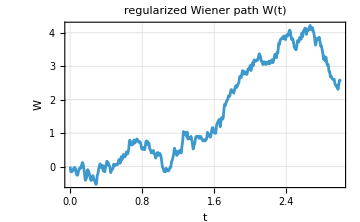
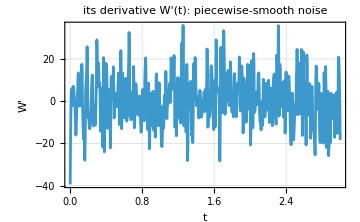

```mathematica
With[{Wf = wienerFun[tfB, dtGenOf[ratesB], 11],
  g = noiseGrid[tfB, dtGenOf[ratesB]]},
 With[{s = Subdivide[0., tfB, 2 (Length[g] - 1)]},
  Row[{
    ListLinePlot[Transpose[{s, Wf[s]}], Frame -> True, GridLines -> Automatic,
     PlotLabel -> "regularized Wiener path W(t)", FrameLabel -> {"t", "W"},
     ImageSize -> Medium], "   ",
    ListLinePlot[Transpose[{s, Wf'[s]}], Frame -> True, GridLines -> Automatic,
     PlotLabel -> "its derivative W'(t): piecewise-smooth noise", FrameLabel -> {"t", "W'"},
     ImageSize -> Medium]}]]]
```

The realized noise spacing h selects the regularized random ODE and controls its bias relative to the white-noise limit. MaxStepSize controls only the numerical integration of that fixed ODE. Capping it below h makes NDSolve resolve each interpolation interval, but neither the cap nor the rate heuristic establishes convergence by itself.

Assemble one trajectory. Build the piecewise-smooth forcing, form the random ODE OverDot[v⃗]=(a⃗)_Strat(v⃗)+(b⃗)_Strat(v⃗)W'_h(t) for the full four-vector, and hand it to NDSolve. If no cap is supplied, use one quarter of the realized noise-grid spacing:

```mathematica
ClearAll[oneTraj];
oneTraj[r_, init_, tf_, dtGen_, seed_, maxstep_ : Automatic, goal_ : Automatic] :=
  Module[{Wf, xx, yy, zz, QQ, t, rhs, eqs, stepCap},
   Wf = wienerFun[tf, dtGen, seed];
   stepCap = Replace[maxstep, Automatic -> noiseStep[tf, dtGen]/4];
   rhs = driftStrat[{xx[t], yy[t], zz[t], QQ[t]}, r] +
     diffStrat[{xx[t], yy[t], zz[t], QQ[t]}, r] Wf'[t];
   eqs = Join[MapThread[#1'[t] == #2 &, {{xx, yy, zz, QQ}, rhs}],
     {xx[0] == init[[1]], yy[0] == init[[2]], zz[0] == init[[3]], QQ[0] == init[[4]]}];
   NDSolveValue[eqs, {xx, yy, zz, QQ}, {t, 0, tf}, MaxStepSize -> stepCap,
    AccuracyGoal -> goal, PrecisionGoal -> goal]];
```

Show one trajectory two ways: the monitored component z(t) against the exact Lindblad mean, and the readout Q(t) it accumulates, both built from the single four-vector solution:

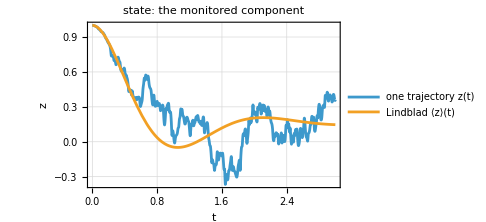
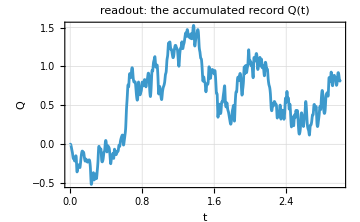

```mathematica
With[{traj = oneTraj[ratesB, initB, tfB, dtGenOf[ratesB], 7, dtGenOf[ratesB]/4],
   lb = lindbladBloch[ratesB, initB[[1 ;; 3]]]},
 Row[{
   Plot[{traj[[3]][t], lb[t][[3]]}, {t, 0, tfB},
    PlotLegends -> Placed[{"one trajectory z(t)", "Lindblad ⟨z⟩(t)"}, Below],
    Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "z"},
    PlotLabel -> "state: the monitored component", ImageSize -> Medium], "   ",
   Plot[traj[[4]][t], {t, 0, tfB},
    Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "Q"},
    PlotLabel -> "readout: the accumulated record Q(t)", ImageSize -> Medium]}]]
```

As one can see, the state path fluctuates around the Lindblad mean, as a single record must, while the readout Q climbs steeply where z is near one and bends as z falls, its √Γ_CI z signal buried under noise. The two panels share one dW, and that is the physical content of a measurement record: the noise written into Q is the same noise that kicked z.

## The ensemble: matching the mean and the spread

A single path tells us little about the law. We therefore retain full trajectories from two finite-step simulations: the built-in StratonovichProcess integrator and the regularized NDSolve route. Their means can be compared with the closed Lindblad solution, while their spreads probe information that the mean cannot see. Agreement is evidence at the stated time steps and sample size; it is not by itself a convergence theorem.

Before any simulation, let's verify the Itô-Stratonovich conversion. If the explicit Stratonovich drift truly carries the correction, its Itô form must be the affine drift a⃗ we encoded as driftIto for the Lindblad reference, with the readout row untouched. Convert the full four-component field and test it against that target, under the physical assumption that the rates are nonnegative (needed only to fold √Γ_CI √Γ_BA into a single root):

```mathematica
Assuming[{Subscript[Γ, "CI"] >= 0, Subscript[Γ, "BA"] >= 0},
 FullSimplify[
  (ItoProcess[StratonovichProcess[{driftStrat[{x, y, z, q}, ratesSym],
        List /@ diffStrat[{x, y, z, q}, ratesSym], {x, y, z, q}},
       {{x, y, z, q}, {x0, y0, z0, q0}}, t]]["Drift"] /. {x[t] -> x, y[t] -> y, z[t] -> z, q[t] -> q})
   == Append[driftIto[{x, y, z}, ratesSym], Sqrt[Subscript[Γ, "CI"]] z]]]
```

True

The equality holds row by row: the Itô form of the Stratonovich SDE we hand NDSolve is exactly the affine drift on all three Bloch rows, with the readout row unchanged, so the correction is carried in full and Q is the same in both calculi.

The trajectories are independent integrations, so the regularized generator below spreads them across local subkernels with ParallelTable, which launches the configured kernels on its first use and ships the Global context definitions to them automatically. The wall-clock gain is set by the machine's core mix and scheduling, typically a factor of a few rather than the kernel count; with no subkernels available the same cells simply evaluate sequentially.

Generate ntraj full trajectories from the built-in StratonovichProcess integrator. Feed it the same four-row Stratonovich field and request the documented order-$3/2$ scalar-noise method rather than the default order-1/2 Euler-Maruyama method. The method order describes asymptotic discretization behavior; it does not remove finite-step bias:

```mathematica
ClearAll[stratRun];
stratRun[r_, init_, tf_, dt_, ntraj_, seed_] :=
  Module[{t, v, proc, td},
   v = {x[t], y[t], z[t], q[t]};
   proc = StratonovichProcess[{driftStrat[v, r], List /@ diffStrat[v, r], v},
     {{x, y, z, q}, init}, t];
   td = BlockRandom[SeedRandom[seed];
     RandomFunction[proc, {0., tf, dt}, ntraj, Method -> "StochasticRungeKuttaScalarNoise"]];
   td["ValueList"]];
```

Generate the same count of regularized trajectories, each NDSolve solution read off on a shared time grid, keeping all four components so the record stays beside the state that produced it. Three arguments carry defaults: the integration-step cap is one quarter of the realized noise spacing, the read-off grid is the noise grid itself, and the solver goals pass to NDSolve unchanged:

```mathematica
ClearAll[regRun];
regRun[r_, init_, tf_, dtGen_, ntraj_, baseSeed_, maxstep_ : Automatic, grid_ : Automatic, goal_ : Automatic] :=
  With[{ms = maxstep /. Automatic -> noiseStep[tf, dtGen]/4,
    g = grid /. Automatic -> noiseGrid[tf, dtGen]},
   ParallelTable[
    With[{tr = oneTraj[r, init, tf, dtGen, baseSeed + i, ms, goal]},
     Transpose[#[g] & /@ tr]],
    {i, ntraj}]];
```

For the harder regimes and the step-size study below we will want only the final values, so reduce each generator to them. The native final Bloch vectors:

```mathematica
ClearAll[stratRef];
stratRef[r_, init_, tf_, dt_, ntraj_, seed_] := stratRun[r, init, tf, dt, ntraj, seed][[All, -1, 1 ;; 3]];
```

And the regularized final Bloch vectors, read off at t_f alone, the cap and the goals defaulting the same way:

```mathematica
ClearAll[ensemble];
ensemble[r_, init_, tf_, dtGen_, ntraj_, baseSeed_, maxstep_ : Automatic, goal_ : Automatic] :=
  regRun[r, init, tf, dtGen, ntraj, baseSeed, maxstep, {tf}, goal][[All, -1, 1 ;; 3]];
```

Run both on the representative case, on the shared grid set by dtGenOf[ratesB]. First the native ensemble:

```mathematica
stratRunB = stratRun[ratesB, initB, tfB, dtGenOf[ratesB], nB, 2024];
```

Then the regularized ensemble on the same grid. Its displayed statistics resolve differences only at Monte-Carlo scale, so the production ensembles pass AccuracyGoal and PrecisionGoal of five to NDSolve; the pathwise identity checks below, where solver error itself is on display, keep the defaults:

```mathematica
regRunB = regRun[ratesB, initB, tfB, dtGenOf[ratesB], nB, 9100, Automatic, Automatic, 5];
```

Average each ensemble over its trajectories and compare the two mean paths of ⟨z⟩ against the single exact Lindblad trajectory:

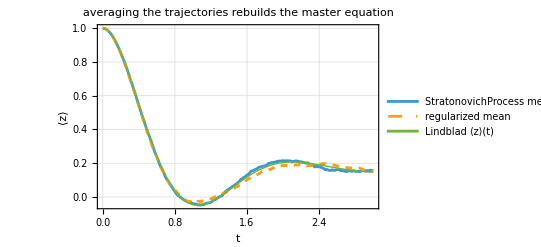

```mathematica
With[{g = noiseGrid[tfB, dtGenOf[ratesB]], lb = lindbladBloch[ratesB, initB[[1 ;; 3]]]},
 ListLinePlot[{
    Transpose[{g, Mean[stratRunB][[All, 3]]}],
    Transpose[{g, Mean[regRunB][[All, 3]]}],
    Transpose[{g, lb[#][[3]] & /@ g}]},
   PlotStyle -> {Automatic, Dashed, Thick},
   PlotLegends -> {"StratonovichProcess mean", "regularized mean", "Lindblad ⟨z⟩(t)"},
   Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "⟨z⟩"},
   PlotLabel -> "averaging the trajectories rebuilds the master equation"]]
```

The plot compares both sampled ensemble means with the exact Lindblad curve over the whole stored grid. In the white-noise theory the ensemble average obeys the master equation exactly; finite ensembles fluctuate around it.

Quantify the largest gap between the regularized mean of z and the Lindblad value anywhere on the grid, in Monte-Carlo standard errors, skipping t=0 (where all paths coincide and the standard error vanishes):

```mathematica
With[{g = Rest[noiseGrid[tfB, dtGenOf[ratesB]]], lb = lindbladBloch[ratesB, initB[[1 ;; 3]]],
  zc = regRunB[[All, 2 ;;, 3]]},
 Max[Abs[Mean[zc] - (lb[#][[3]] & /@ g)]/(StandardDeviation[zc]/Sqrt[nB])]]
```

2.8495

This is the largest pointwise standardized gap on the stored grid. Because it is a maximum over many correlated times, ordinary one-, two-, or three-standard-error thresholds do not calibrate it as a simultaneous test. Use it as a scale diagnostic; a formal whole-curve test would require the sampling distribution of the maximum, for example from an independent bootstrap.

The mean sees only the drift, so it is a weak test. The measurement backaction lives in the standard deviation of the final Bloch vector, its spread across the ensemble, compared across the two routes:

```mathematica
TableForm[
 Transpose[{StandardDeviation[stratRunB[[All, -1, 1 ;; 3]]],
   StandardDeviation[regRunB[[All, -1, 1 ;; 3]]]}],
 TableHeadings -> {{"Spread in x", "Spread in y", "Spread in z"}, {"Stratonovich", "Regularized"}}]
```

-Graphics-

The displayed spreads provide a diffusion-sensitive comparison between the two finite-step routes. All three components fluctuate: x starts at zero and its mean stays there, yet the backaction quadrature feeds its fluctuations from y.

The sample spread is itself uncertain. A large-sample delta-method estimate is SE(s)≈√((m_4-s^4)/(4 s^2 n)), where m_4 is the fourth central moment. The plug-in code below estimates the moments from the same sample. It is an asymptotic scale estimate, not an exact finite-sample error bar.

Encode SE, the error bar of one spread, both moments read off the sample:

```mathematica
ClearAll[sdErr];
sdErr[x_] := With[{v = CentralMoment[x, 2]}, Sqrt[(CentralMoment[x, 4] - v^2)/(4 v Length[x])]];
```

Compare the Stratonovich and regularized spreads by dividing their absolute difference by their combined standard error,

G=(s_Strat-s_reg)/(√(SE(s_Strat)^2+SE(s_reg)^2)),

so G=1 means that the two spreads differ by one combined standard error. Encode this statistic:

```mathematica
ClearAll[spreadGap];
spreadGap[x1_, x2_] := Abs[StandardDeviation[x1] - StandardDeviation[x2]]/
   Sqrt[sdErr[x1]^2 + sdErr[x2]^2];
```

Read each component's gap in those units:

```mathematica
AssociationThread[{"Spread gap in x", "Spread gap in y",
  "Spread gap in z"},
 spreadGap[stratRunB[[All, -1, 1 ;; 3]], regRunB[[All, -1, 1 ;; 3]]]]
```

<|Spread gap in x→1.34435,Spread gap in y→0.863418,Spread gap in z→0.555244|>

The returned numbers express each spread difference in approximate combined-standard-error units. They are useful diagnostics, but they are not a distribution-free hypothesis test and do not justify the phrase “statistically indistinguishable” without a calibrated sampling analysis.

The conditional state must stay in the unit Bloch ball. On its boundary the radial diffusion vanishes, (x,y,z)·b⃗=√Γ_CI z(1-x^2-y^2-z^2)=0. The remaining stochastic-invariance condition is that the Itô generator applied to r^2=x^2+y^2+z^2 point inward or tangent there. Its boundary value is 2(x,y,z)·a⃗+b⃗·b⃗:

(ℒ(r^2)|)_(r=1)=(1-z^2) (Γ_CI+Γ_BA-2(Γ_d+γ_ϕ))-γ_1(1-z)^2,

where ℒ is the Itô generator.

Verify that closed form, substituting a point on the sphere and subtracting the claim:

```mathematica
With[{b3 = diffStrat[{x, y, z, q}, ratesSym][[1 ;; 3]]},
 Simplify[((2 {x, y, z} . driftIto[{x, y, z}, ratesSym] + b3 . b3) /.
     {x -> Sqrt[1 - z^2] Cos[ϕ], y -> Sqrt[1 - z^2] Sin[ϕ]}) -
   ((1 - z^2) (ratesSym[[1]] + ratesSym[[2]] - 2 (ratesSym[[3]] + ratesSym[[4]])) -
     ratesSym[[5]] (1 - z)^2)]]
```

0

The subtraction cancels identically. The relaxation term is nonpositive and vanishes quadratically at the ground pole, whereas the measurement term is linear in 1-z near that pole. Consequently the generator is inward or tangent at every boundary point if and only if Γ_CI+Γ_BA≤2(Γ_d+γ_ϕ). Under nonnegative rates and the usual existence assumptions, this is the Bloch-ball invariance condition for this SDE. Every ensemble rate set below satisfies it; one single-path example deliberately violates it. The following maximum is only a numerical spot-check of the regularized solver:

```mathematica
Max[Map[Norm, regRunB[[All, All, 1 ;; 3]], {2}]]
```

1.

The radius sits at one to within a hair, with no projection step. Read this as a spot-check of positivity, not a proof of it: it samples one ensemble on a fixed grid from a state that began on the surface. Violate the admissibility condition, which for a detector means η>1+γ_ϕ/Γ_d, more information extracted than the dephasing paid for, and the equation stops being a valid unraveling: the trajectory can leave the ball, and its coordinates no longer describe a density matrix. That failure is one cell away. Fix rates that fail the check, twice the information the dephasing supplies, start on the sphere away from the pole where the closed form above makes the flux point outward, and read the largest radius one path reaches:

```mathematica
With[{ratesBad = {2., 0., 0.5, 0., 1., 0.}},
 With[{tr = oneTraj[ratesBad, {0.8, 0., 0.6, 0.}, 1., dtGenOf[ratesBad], 5, dtGenOf[ratesBad]/4]},
  Max[Norm /@ Transpose[#[Subdivide[0., 1., 200]] & /@ tr[[1 ;; 3]]]]]]
```

1.02473

The radius runs past one. At the chosen initial boundary point the radial diffusion is zero while the radial generator points outward, so the model immediately violates the invariance condition. The equation still integrates; what fails is its interpretation as a density-matrix trajectory.

The boundary is just as sharp from the inside. Saturate the condition with no relaxation and no intrinsic dephasing, γ_1=γ_ϕ=0 with both quadratures on and the drive on too, Γ_CI+Γ_BA=2 Γ_d exactly, and the closed form above vanishes identically: the sphere itself is invariant, so a pure state stays pure along every single trajectory, not merely on average. Start a path on the sphere and read how far it ever leaves:

```mathematica
With[{rPure = {0.352, 0.4, 0.376, 0., 0., 3.}},
 With[{tr = oneTraj[rPure, {0.6, 0., 0.8, 0.}, 3., dtGenOf[rPure], 5, dtGenOf[rPure]/4],
   s = Subdivide[0., 3., 400]},
  Max[Abs[Norm /@ Transpose[#[s] & /@ tr[[1 ;; 3]]] - 1]]]]
```

5.7942×10^-6

The radius sticks to the sphere at solver error, the sharpest test of the diffusion's scale in the document: a noise term wrong by any factor would walk the path off the sphere at once. On the boundary, positivity is not an inequality respected but an equality enforced.

## The readout: the average signal and the shared noise

We carried the readout Q beside the state through every run but have only looked at the state. Turn to the record itself. Taking the mean of dQ=√Γ_CI z dt+dW and using ⟨dW⟩=0, the average record is the integrated signal,

⟨Q(t)⟩=√Γ_CI∫_0^t ⟨z(s)⟩ ds,

a closed prediction we already hold, since ⟨z⟩ is the Lindblad mean. And the records are already in hand: every stored trajectory carries Q as its fourth component, so slice the record ensemble out of the same run whose state we just averaged:

```mathematica
recQB = regRunB[[All, All, 4]];
```

The prediction is itself a closed form, not a quadrature: append u'=√Γ_CI ⟨z⟩ to the affine system and let DSolve integrate it exactly:

```mathematica
ClearAll[qpredB];
qpredB = Module[{sol, xf, yf, zf, uf, t},
   sol = DSolve[Join[MapThread[#1'[t] == #2 &, {{xf, yf, zf}, driftIto[{xf[t], yf[t], zf[t]}, ratesB]}],
       {uf'[t] == Sqrt[ratesB[[1]]] zf[t], xf[0] == initB[[1]], yf[0] == initB[[2]],
        zf[0] == initB[[3]], uf[0] == 0}], {xf, yf, zf, uf}, t] // First;
   Function[tt, Re[uf[tt] /. sol]]];
```

Overlay the ensemble-averaged record on that prediction:

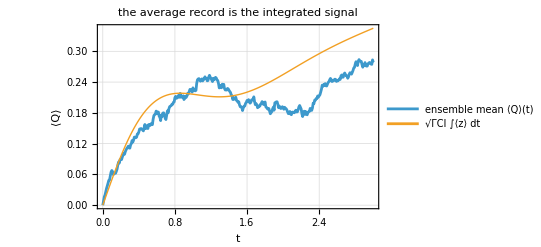

```mathematica
With[{g = noiseGrid[tfB, dtGenOf[ratesB]]},
 ListLinePlot[{Transpose[{g, Mean[recQB]}], Transpose[{g, qpredB /@ g}]},
  PlotStyle -> {Automatic, Thick},
  PlotLegends -> {"ensemble mean ⟨Q⟩(t)", "√ΓCI ∫⟨z⟩ dt"},
  Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "⟨Q⟩"},
  PlotLabel -> "the average record is the integrated signal"]]
```

As expected, the mean record follows the integrated mean signal. Each trajectory satisfies

Q_i(t)=√Γ_CI∫_0^t z_i(s) ds+W_i(t),

so averaging n_traj trajectories gives

Q̄(t)=√Γ_CI∫_0^t z̄(s) ds+W̄(t).

In the infinite-ensemble limit, z̄→⟨z⟩ and W̄→0, recovering the exact prediction ⟨Q(t)⟩=√Γ_CI∫_0^t ⟨z(s)⟩ ds. At finite n_traj, the averaged Wiener path has standard deviation √(t/n_traj), so it leaves a Brownian-like residual wander rather than cancelling exactly. For example, at t=3 with n_traj=600, this direct noise contribution has a standard deviation of about 0.071. The complete discrepancy also includes sampling fluctuations in z̄, so its appropriate error scale is the standard error of the mean record, s_Q(t)/√n_traj. The signal survives averaging, while the statistical fluctuations shrink as 1/√n_traj.

Quantify the agreement at each nonzero grid time t_j with the standardized residual

Z_Q(t_j)=(Q̄(t_j)-Q_pred(t_j))/(s_Q(t_j)/√n_traj),

where Q_pred(t_j)=√Γ_CI∫_0^t_j ⟨z(s)⟩ ds and s_Q(t_j) is the sample standard deviation of the records at that time. The denominator therefore includes both the direct Wiener noise and the trajectory-to-trajectory variation of the integrated signal. Omit t=0, where every record is fixed at zero and the standard error vanishes, and report the largest standardized residual on the sampled grid:

```mathematica
With[{g = Rest[noiseGrid[tfB, dtGenOf[ratesB]]], qc = recQB[[All, 2 ;;]]},
 Max[Abs[Mean[qc] - (qpredB /@ g)]/(StandardDeviation[qc]/Sqrt[nB])]]
```

1.65117

The result measures the largest pointwise discrepancy in standard-error units. Because the maximum is taken over correlated times, pointwise Gaussian thresholds do not give its false-alarm probability. It is a diagnostic of scale, not a calibrated simultaneous test and not a claim about unsampled times.

The record's spread deserves the same two-route treatment as the state's, and the native ensemble has been carrying the fourth row all along; read its final-Q spread against the regularized ensemble's, in the same units as before:

```mathematica
spreadGap[stratRunB[[All, -1, 4]], recQB[[All, -1]]]
```

0.900995

The final-record spread supplies the corresponding diffusion-sensitive comparison for the fourth row. Here the two finite samples differ on the scale estimated above.

The average removed the noise, but a single record still carries it, and carries a specific one. Since dQ-√Γ_CI z dt=dW exactly, subtracting the integrated signal from one record must return the very Wiener path that drove the state. Build one trajectory, strip its signal, and overlay the remainder on its driving path W(t):

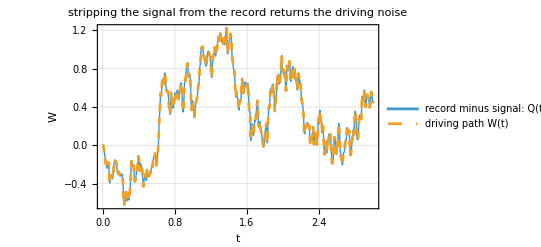

```mathematica
With[{r = ratesB, dt = dtGenOf[ratesB], seed = 7},
 With[{Wf = wienerFun[tfB, dt, seed], traj = oneTraj[r, initB, tfB, dt, seed, dt/4]},
  Module[{u, t, zint},
   zint = NDSolveValue[{u'[t] == traj[[3]][t], u[0] == 0.}, u, {t, 0, tfB}];
   Plot[{traj[[4]][t] - Sqrt[r[[1]]] zint[t], Wf[t]}, {t, 0, tfB},
    PlotStyle -> {Thick, Dashed},
    PlotLegends -> Placed[{"record minus signal: Q(t) - √ΓCI ∫z dt", "driving path W(t)"}, Below],
    Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "W"},
    PlotLabel -> "stripping the signal from the record returns the driving noise"]]]]
```

Notice that the stripped record lands on the driving path to the width of the line. This is the physical content of a measurement made literal: the fluctuations in the record are not merely correlated with the noise that kicked the state, they are that noise. The observer reads √Γ_CI∫z ds as signal; the remainder is the single innovation dW the detector wrote into the record and the backaction at once.

Rather than trust the line width, put a number on it, the largest gap between the stripped record and the driving path across the window; define the residual once, its solver goals adjustable, and read it at the default tolerance:

```mathematica
ClearAll[recordResidual];
recordResidual[goal_] := With[{r = ratesB, dt = dtGenOf[ratesB], seed = 7},
   With[{Wf = wienerFun[tfB, dt, seed], traj = oneTraj[r, initB, tfB, dt, seed, dt/4, goal]},
    Module[{u, t, zint},
     zint = NDSolveValue[{u'[t] == traj[[3]][t], u[0] == 0.}, u, {t, 0, tfB},
       AccuracyGoal -> goal, PrecisionGoal -> goal];
     With[{s = Subdivide[0., tfB, 1000]},
      Max[Abs[traj[[4]][s] - Sqrt[r[[1]]] zint[s] - Wf[s]]]]]]];
recordResidual[Automatic]
```

1.91758×10^-6

The same ODE defines Q'=√Γ_CI z+W', so this is a self-consistency check, not an independent validation of the route. Its residual combines the numerical errors of the four-component solve and the auxiliary integral. Rerun the same trajectory with tighter goals:

```mathematica
recordResidual[10]
```

1.69006×10^-8

The residual decreases when the requested goals are tightened, as expected for integration error. The exact regularized ODE satisfies the identity; the reported nonzero residual is numerical.

One regime makes the tie between the monitored population and its record explicit. Switch off relaxation and drive, γ_1=Ω_x=0. Phase backaction and transverse dephasing still affect x and y, but not z. Dividing the Stratonovich z row by 1-z^2 and using the ordinary chain rule gives d arctanh z=Γ_CI z dt+√Γ_CI dW=√Γ_CI dQ. Therefore

z(t)=tanh (arctanh z_0+√Γ_CI ).

The formula determines the monitored component z, not by itself the entire Bloch vector. First check the differential identity on the symbolic flow, with the formal w standing in for the regularized noise:

```mathematica
With[{rFree = ReplacePart[ratesSym, {5 -> 0, 6 -> 0}]},
 Simplify[(driftStrat[{x, y, z, q}, rFree][[3]] + diffStrat[{x, y, z, q}, rFree][[3]] w)/(1 - z^2) -
   Sqrt[rFree[[1]]] (driftStrat[{x, y, z, q}, rFree][[4]] + diffStrat[{x, y, z, q}, rFree][[4]] w)]]
```

0

The identity holds with Γ_BA,Γ_d,γ_ϕ symbolic: only relaxation or a drive breaks this closed relation between z and Q. The numerical example uses Q(0)=0 and a bare-measurement rate set on the admissibility boundary, Γ_CI=2 Γ_d with γ_ϕ=0:

```mathematica
ClearAll[rG, tanhResidual];
rG = {0.352, 0., 0.176, 0., 0., 0.};
tanhResidual[goal_] := With[{z0 = 0.6},
   With[{tr = oneTraj[rG, {0., 0., z0, 0.}, tfB, dtGenOf[rG], 11, dtGenOf[rG]/4, goal],
     s = Subdivide[0., tfB, 1000]},
    Max[Abs[tr[[3]][s] - Tanh[ArcTanh[z0] + Sqrt[rG[[1]]] tr[[4]][s]]]]]];
tanhResidual[Automatic]
```

1.17008×10^-6

Tighten the goals and the violation must follow the solver, not the noise grid:

```mathematica
tanhResidual[10]
```

4.51974×10^-8

It falls with the tolerance. For each regularized path, the ordinary chain rule makes the identity exact independently of the white-noise limit. In this regime the monitored coordinate z is the record read through a tanh.

## The two time steps: which one sets the answer

The simulation uses two distinct time increments: the noise-grid spacing Δ t_gen and NDSolve's maximum integration step. Which one controls the numerical result? Test the integration step first by holding the noise grid, the noise realizations, and the solver goals fixed, then comparing the final-z mean and spread for two step caps: Δ t_gen/4 and 10Δ t_gen. The first row uses the stored ensemble; the second recomputes the same trajectories with the relaxed step cap:

```mathematica
TableForm[
 Map[{Mean[#][[3]], StandardDeviation[#][[3]]} &,
  {regRunB[[All, -1, 1 ;; 3]],
   ensemble[ratesB, initB, tfB, dtGenOf[ratesB], nB, 9100, 10 dtGenOf[ratesB], 5]}],
 TableHeadings -> {{"step Δt_gen/4",
    "step 10 Δt_gen"}, {"mean z", "spread z"}}]
```

-Graphics-

The same seeds generate the same interpolated paths in both rows. For this parameter set and these observables, relaxing the cap moves the mean and the spread by far less than their Monte-Carlo uncertainties; the residual difference between the rows is solver error at the production goals, not a noise-discretization effect. This is a case-specific sensitivity check, not evidence that MaxStepSize is generally irrelevant.

The regularization dial is Δ t_gen, and the native StratonovichProcess ensemble supplies a finite-step reference. Read its final-z mean:

```mathematica
Mean[stratRunB[[All, -1, 3]]]
```

0.154528

and its final-z spread, the number the regularized route must reproduce as the grid tightens:

```mathematica
StandardDeviation[stratRunB[[All, -1, 3]]]
```

0.233106

Check the native integrator at three step sizes. The runs use the same integer seed, but changing the step changes how random numbers are consumed, so they should be treated as separate Monte Carlo samples rather than pathwise-coupled trajectories:

```mathematica
natZB = Prepend[Table[stratRef[ratesB, initB, tfB, dtGenOf[ratesB]/f, nB, 2024][[All, 3]],
    {f, {2, 4}}], stratRunB[[All, -1, 3]]];
TableForm[Transpose[{dtGenOf[ratesB]/{1, 2, 4}, StandardDeviation /@ natZB}],
 TableHeadings -> {None, {"dt", "spread z"}}]
```

-Graphics-

Read the two refined rows as distances from the working-step row, in units of the estimates' sampling errors in quadrature:

```mathematica
TableForm[{spreadGap[#, First[natZB]]} & /@ Rest[natZB],
 TableHeadings -> {{"dt/2", "dt/4"}, {"Spread gap in z"}}]
```

-Graphics-

The refined estimates show no resolved trend relative to their Monte Carlo uncertainty. That supports using the working step as a practical reference at this sample size, but it does not prove convergence.

Now sweep Δ t_gen from coarse to fine, the integrator step held below it, and tabulate the regularized mean and spread of the final z against the grid step:

```mathematica
nSweep = 300;
sweepZB = Table[ensemble[ratesB, initB, tfB, tfB/k, nSweep, 6000, Automatic, 5][[All, 3]], {k, {6, 12, 25, 100, 400}}];
TableForm[Transpose[{N[tfB/{6, 12, 25, 100, 400}], Mean /@ sweepZB, StandardDeviation /@ sweepZB}],
 TableHeadings -> {None, {"Δt_gen", "mean z", "spread z"}}]
```

-Graphics-

The table shows how the estimated mean and spread vary across the sampled noise meshes. Put the mean column in pointwise Monte Carlo standard-error units relative to the exact Lindblad value:

```mathematica
With[{lbz = lindbladBloch[ratesB, initB[[1 ;; 3]]][tfB][[3]]},
 TableForm[
  Transpose[{N[tfB/{6, 12, 25, 100, 400}],
    Abs[Mean[#] - lbz]/(StandardDeviation[#]/Sqrt[nSweep]) & /@ sweepZB}],
  TableHeadings -> {None, {"noise step", "gap of the mean from Lindblad, in standard errors"}}]]
```

-Graphics-

The table resolves no systematic mean bias at this sample size. The spread is more sensitive to the regularization mesh, as expected because the affine mean is diffusion-blind. A finite sweep can bound effects at its sampled meshes; it cannot establish the h→0 limit.

## A strong readout: the same route where the drift is large

The gap between the Itô and Stratonovich drifts scales with the measurement rate, so a strong informative readout is the stringent test of feeding NDSolve the Stratonovich form. Fix a strong readout from a tilted start, again a four-vector with the readout zeroed; the rates are again quantum-limited (η=1), with the intrinsic dephasing supplying the slack in the admissibility check:

```mathematica
ratesS = {7., 1., 4., 1., 1., 3.}; initS = {0.6, 0., 0.6, 0.}; tfS = 1.5; nS = 600;
ratesS[[1]] + ratesS[[2]] <= 2 (ratesS[[3]] + ratesS[[4]])
```

True

Read its efficiency:

```mathematica
efficiency[ratesS]
```

1.

Run the native reference for the strong case:

```mathematica
stratS = stratRef[ratesS, initS, tfS, dtGenOf[ratesS], nS, 3030];
```

Run the regularized ensemble for the strong case:

```mathematica
regS = ensemble[ratesS, initS, tfS, dtGenOf[ratesS], nS, 5300, Automatic, 5];
```

Compare the mean of the final Bloch vector across the three routes:

```mathematica
TableForm[
  Transpose[{lindbladBloch[ratesS, initS[[1 ;; 3]]][tfS], Mean[stratS],
   Mean[regS]}],
  TableHeadings -> {{"Mean of x", "Mean of y",
    "Mean of z"}, {"Lindblad", "Stratonovich", "regularized"}}]
```

-Graphics-

As one can see, the regularized mean still tracks the exact value in every row where the correction is large; the x row has decayed from its initial tilt toward zero under the transverse decay, and all three routes agree on the small residual. Compare the spread across the two routes:

```mathematica
TableForm[
  Transpose[{StandardDeviation[stratS], StandardDeviation[regS]}],
  TableHeadings -> {{"SD of x", "SD of y", "SD of z"}, {"Stratonovich", "regularized"}}]
```

-Graphics-

As expected, the spreads agree closely where the Stratonovich correction is largest. Put the sampling scale on all three components again:

```mathematica
TableForm[{spreadGap[stratS, regS]},
 TableHeadings -> {{"Spread gap"}, {"x", "y", "z"}}]
```

-Graphics-

All three gaps sit at the sampling scale even at strong coupling. See the final-z marginal agree, the regularized histogram against the native Stratonovich reference:

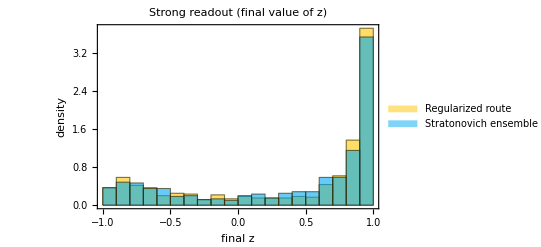

```mathematica
Histogram[{regS[[All, 3]], stratS[[All, 3]]}, 24, "PDF",
  Frame -> True, FrameLabel -> {"final z", "density"},
  PlotLabel -> "Strong readout (final value of z)", 
 PlotLegends -> {"Regularized route", "Stratonovich ensemble"}]
```

This confirms that the regularized histogram sits on top of the native Stratonovich reference: the route reproduces the final-z marginal, not merely its mean, even where the drift correction is strong.

Repeat the finite mesh-sensitivity check in the strong-readout case, where the conversion correction is larger:

```mathematica
sweepZS = Table[ensemble[ratesS, initS, tfS, tfS/k, nSweep, 6600, Automatic, 5][[All, 3]], {k, {120, 240, 480}}];
TableForm[Transpose[{N[tfS/{120, 240, 480}], StandardDeviation /@ sweepZS}],
 TableHeadings -> {None, {"Δt_gen", "SD in z"}}]
```

-Graphics-

Now read each row as a distance from the native strong-case spread, in units of the two estimates' sampling errors in quadrature:

```mathematica
TableForm[
 Transpose[{N[tfS/{120, 240, 480}], spreadGap[#, stratS[[All, 3]]] & /@ sweepZS}],
 TableHeadings -> {None, {"noise step", "gap of the spread from the native run, in sampling errors"}}]
```

-Graphics-

These three estimates show no resolved trend beyond their Monte Carlo scale. That supports the working mesh for the displayed observable and sample size; it does not certify the forty-interval heuristic for other rates, initial states, observables, or accuracy targets.

## What is now true

The monitored qubit and its accumulated readout form one four-component SDE driven by one scalar noise. To make an equation NDSolve can accept, first convert the target Itô drift to the equivalent Stratonovich drift, then replace the Wiener path by a continuous piecewise-cubic approximation W_h. NDSolve receives the random ODE (v̇)_h=a_Strat(v_h)+b(v_h)W'_h. Under the scalar-noise Wong-Zakai conditions, its solution approaches the target Itô process through the equivalent Stratonovich representation as h→0.

The exact algebra is stronger than the numerical evidence: the Itô conversion, Lindblad generator, readout identity, and Bloch-ball flux all reduce symbolically to the claimed formulas. The simulations are finite-resolution checks. Their means and spreads agree with the stated references at the displayed scales, but regularization bias, stochastic-integrator bias, ODE error, and Monte Carlo uncertainty remain distinct error sources.

Integrating the readout beside the state costs one extra equation and preserves the shared innovation explicitly. Its ensemble mean is √Γ_CI∫⟨z⟩ds; subtracting the pathwise signal returns the same regularized Wiener path that drives the state; and with drive and relaxation absent, the monitored coordinate is a closed tanh function of the record. The Bloch-vector interpretation requires Γ_CI+Γ_BA≤2(Γ_d+γ_ϕ); outside that condition the equation may still integrate, but its trajectories need not represent density matrices.

## Acknowledgment

Thanks to Jose M. Martin-Garcia (Wolfram R&D) for suggesting this approach as a way to simulate random processes.